# Wavelet Proposal

## Haar wavelets

Piecewise[{{-1, 1/2<x<1}, {1, 0<x<1/2}, {0, True}}]

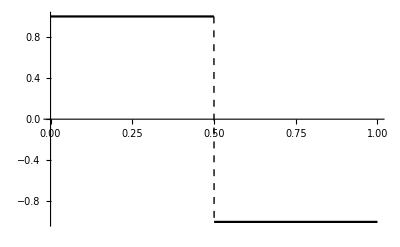

Piecewise[{{-1, 3/2<x<2}, {1, 1<x<3/2}, {0, True}}]

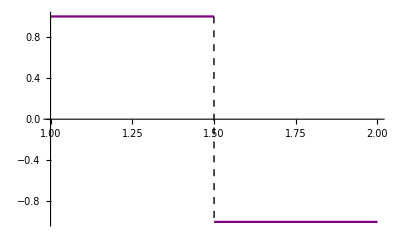

Piecewise[{{-1, 15/16<x<1}, {1, 7/8<x<15/16}, {0, True}}]

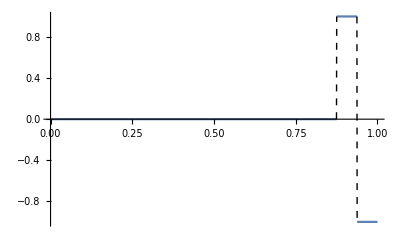

2

12

Piecewise[{{2, 3<x<25/8}, {-2, 25/8<x<13/4}, {0, True}}]

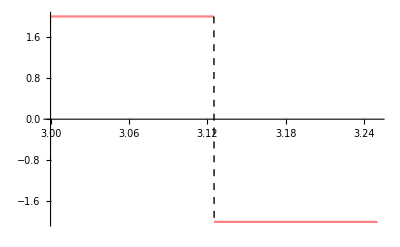

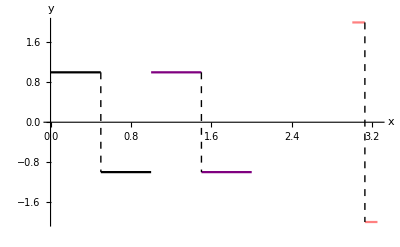

```mathematica
P=Piecewise[{{-1, 1/2<x<1}, {1, 0<x<1/2}}]
p1 = Plot[P,{x,0,1}, ExclusionsStyle->Dashed,PlotStyle->Black]
P01=Piecewise[{{-1, 1+1/2<x<1+1}, {1, 1<x<1+1/2}}]
p01 = Plot[P01,{x,1,2}, ExclusionsStyle->Dashed,PlotStyle->Purple]
P34=Piecewise[{{-1, (1/2+7)/8<x<1}, {1, 7/8<x<(1/2+7)/8}}]
p34 = Plot[P34,{x,0,1}, ExclusionsStyle->Dashed]
j=2
k=12
h=Piecewise[{{2^(j/2), (k/(2^j))<x<(1/2+k)/(2^j)}, {-2^(j/2), (1/2+k)/(2^j)<x<(1+k)/(2^j)}}]
h1 = Plot[h,{x,3,13/4}, ExclusionsStyle->Dashed,PlotLegends->Automatic,PlotStyle->Pink]

plot = Show[p1,p01,h1,PlotRange->All, AxesLabel->{"x","y"}]
```

```mathematica
Blue
```

```mathematica
Legended[plot,LineLegend[{Black,Purple,Pink},{ψ,Subscript[ψ,"0,1"],Subscript[ψ,"2,12"]}]]
```

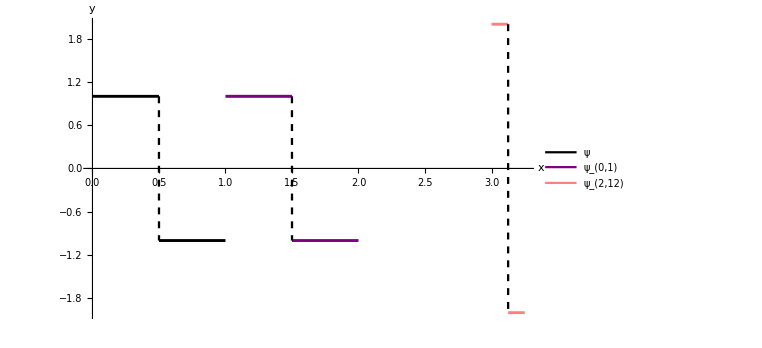

## Example of Function Approximations

ⅇ^-x Sin[2 π x]

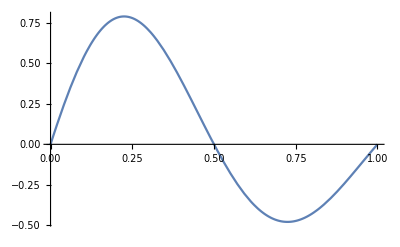

```mathematica
f = E^-x Sin[2 Pi x]
Plot[f,{x,0,1}]
```

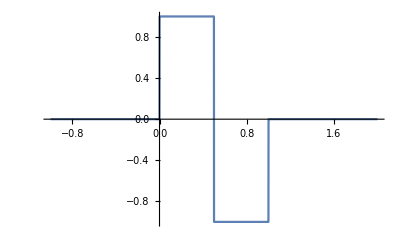

```mathematica
Plot[WaveletPsi[HaarWavelet[],x],{x,-1,2},Exclusions->None]
```

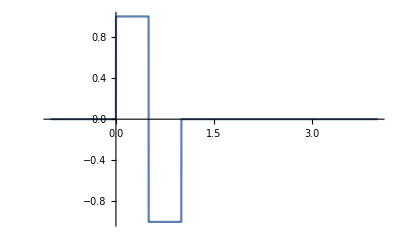

```mathematica
Plot[WaveletPsi[HaarWavelet[],x],{x,-1,4},Exclusions->None]
```

## Some graphs

```mathematica
ψ[x_,j_,k_]:=2^(j/2) WaveletPsi[HaarWavelet[],2^j x-k]
```

```mathematica
Plot[Evaluate[Table[ψ[x,j,k],{j,{0,1,2}},{k,{0,2,3}}]],{x,0,6},Filling->Axis,PlotLegends->"Expressions",AxesLabel->Automatic]
```

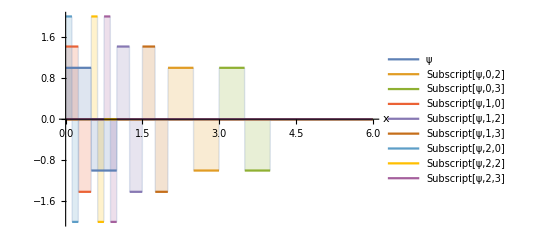

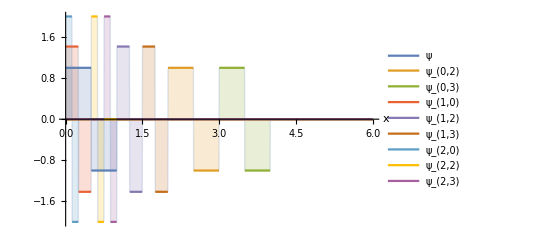

Approximations

```mathematica
Manipulate[Module[{phi,g,a},phi[x_]=Piecewise[{{1,0≤x<1}},0];
g[x_,k_,j_]=2^(j/2)phi[2^j x-k];
a[k_,j_]=∫_(k/2^j)^((k+1)/2^j) f*2^(j/2)ⅆx;
Plot[{f,Sum[a[k,j] g[x,k,j],{k,0,2^j-1}]},{x,0,1},PlotPoints->70,Exclusions->None,PlotRange->{0,1},ImageSize->{500,300}]],{{j,2,"level j"},0,5,1,Appearance->"Labeled"},{{f,ⅇ^-x,"function"},{ⅇ^-x->TraditionalForm[e^-x],x^2->TraditionalForm[x^2],Sin[π x]->TraditionalForm[Sin[π x]],(1+Sin[6 π x])/2->TraditionalForm[(1+Sin[6 π x])/2]}},TrackedSymbols:>True]
```

```mathematica
Manipulate[Module[{phi,g,a},phi[x_]=Piecewise[{{1,0≤x<1/2},{-1,1/2 ≤ x< 1}},0];
g[x_,k_,j_]=2^(j/2)phi[2^j x-k];
a[k_,j_]=∫_-100^100 f* g ⅆx;
Plot[{f,Sum[Sum[a[k,j] * g[x,k,j] ,{k,0,2^j-1}],{j,0,n-1}]},{x,0,1},PlotPoints->70,Exclusions->None,PlotRange->{0,1},ImageSize->{500,300}]],{{n,2,"level n"},0,5,1,Appearance->"Labeled"},{{f,ⅇ^-x,"function"},{ⅇ^-x->TraditionalForm[e^-x],x^2->TraditionalForm[x^2],Sin[π x]->TraditionalForm[Sin[π x]],(1+Sin[6 π x])/2->TraditionalForm[(1+Sin[6 π x])/2]}},TrackedSymbols:>True]
```

```mathematica
Manipulate[Module[{phi,g,a},phi[x_]=Piecewise[{{1,0≤x<1/2},{-1,1/2 ≤ x< 1}},0];
g[x_,k_,j_]=2^(j/2)phi[2^j x-k];
a[k_,j_]=∫_(-∞)^∞ f  gⅆx;
Plot[{f,Sum[Sum[a[k,j] * g[x,k,j],{k,0,2^j-1}],{j,0,n-1}]  },{x,0,1},PlotPoints->70,Exclusions->None,PlotRange->{0,1},ImageSize->{500,300}]],{{n,2,"level n"},0,5,1,Appearance->"Labeled"},{{f,x^2,"function"},{x^2->TraditionalForm[x^2],Sin[π x]->TraditionalForm[Sin[π x]],(1+Sin[6 π x])/2->TraditionalForm[(1+Sin[6 π x])/2]}},TrackedSymbols:>True]
```

Integrate::idiv: Integral of g$44154 x^2 does not converge on {-∞,∞}.

Integrate::ilim: Invalid integration variable or limit(s) in {0.0000145072,-∞,∞}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

NIntegrate::itraw: Raw object 0.0000145072 cannot be used as an iterator.

NIntegrate::itraw: Raw object 0.0145073 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

```mathematica
Manipulate[Module[{phi,g,a},phi[x_]=Piecewise[{{1,0≤x<1/2},{-1,1/2 ≤ x< 1}},0];
g[x_,k_,j_]=2^(j/2)phi[2^j x-k];
a[k_,j_]=∫_(-∞)^∞ f  gⅆx;
Plot[{f,Sum[Sum[a[k,j] * g[x,k,j],{k,0,2^j-1}],{j,0,n-1}]  },{x,0,1},PlotPoints->70,Exclusions->None,PlotRange->{0,1},ImageSize->{500,300}]],{{n,2,"level n"},0,5,1,Appearance->"Labeled"},{{f,x^2,"function"},{x^2->TraditionalForm[x^2],Sin[π x]->TraditionalForm[Sin[π x]],(1+Sin[6 π x])/2->TraditionalForm[(1+Sin[6 π x])/2]}},TrackedSymbols:>True]
```

```mathematica
}
```

Integrate::idiv: Integral of g$45216 x^2 does not converge on {-∞,∞}.

Integrate::ilim: Invalid integration variable or limit(s) in {0.0000145072,-∞,∞}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

NIntegrate::itraw: Raw object 0.0000145072 cannot be used as an iterator.

NIntegrate::itraw: Raw object 0.0145073 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

```mathematica
Manipulate[Module[{phi,g,a},phi[x_]=Piecewise[{{1,0≤x<1}},0];
g[x_,k_,j_]=2^(j/2)phi[2^j x-k];
a[k_,j_]=∫_(k/2^j)^((k+1)/2^j) f*2^(j/2)ⅆx;
Plot[{f,Sum[a[k,j] g[x,k,j],{k,0,2^j-1}]},{x,0,1},PlotPoints->70,Exclusions->None,PlotRange->{0,1},ImageSize->{500,300}]],{{j,2,"level j"},0,5,1,Appearance->"Labeled"},{{f,x^2,"function"},{x^2->TraditionalForm[x^2]}},TrackedSymbols:>True]
```